units
P->[Debye]/V[nm]^3=(0.021 M_i[e nm])/V[nm^3]=(0.021 M_i->Data)/(V->117.649)[e/nm^2]=0.00018*M_i->Data [e/nm^2]
P_lnr->[Debye]/V[nm]^3+(E/(k_B T V)[Debye])^2=0.00018*M_i->Data [e/nm^2]+[V/nm]/(1.38*10^-23[J/K]*298[K]*(117.649[nm])^3)((0.021)^2[e nm])^2*E*DATA=0.00018*M_i->Data [e/nm^2]+[V]/(48382*10^-23*([J][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+[V]/(48382*10^-23*([V][C][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+1/(48382*10^-23*([C][nm])^2)(0.021)^2[e^2]*E*DATA=0.00018*M_i->Data [e/nm^2]+1/(48382*10^-23*1/1.602(10^19[e][nm])^2)((0.021)^2[e])^2*E*DATA=0.00018*M_i->Data [e/nm^2]+(0.021)^2/(30201*10^-4*[nm]^2)[e]*E*DATA=0.00018*M_i->Data [e/nm^2]+0.00015[e/nm^2]*E*DATA

```mathematica
data=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.0-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
pol=(Mean[(data[[All,5]])^2]-((Mean[data[[All,2]]])^2+(Mean[data[[All,3]]])^2+(Mean[data[[All,4]]])^2))*0.000862793851593755`+1;
mnsq=Mean[(data[[All,5]])^2];
mvc={Mean[data[[All,2]]],Mean[data[[All,3]]],Mean[data[[All,4]]]};
polzero=0.000012947*mvc;
erroremsq=StandardDeviation[(data[[All,5]]*0.021)^2]/Sqrt[Length[data[[All,5]]]];
errormx=StandardDeviation[(data[[All,2]]*0.021)]/Sqrt[Length[data[[All,2]]]];
errormy=StandardDeviation[(data[[All,3]]*0.021)]/Sqrt[Length[data[[All,3]]]];
errormz=StandardDeviation[(data[[All,4]]*0.021)]/Sqrt[Length[data[[All,4]]]];
P=0.00018*mvc
```

{-0.000489803,-0.000291039,-0.000108348}

```mathematica
erropolzeroef={errormx/1622*(1-2*Mean[data[[All,2]]]),errormy/1622*(1-2*Mean[data[[All,3]]]),errormz/1622*(1-2*Mean[data[[All,4]]])}
```

{0.0000976475,0.000063731,0.0000320552}

```mathematica
data1e6=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-6-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef6=Mean[(data1e6[[All,5]])^2];
mvcef6={Mean[data1e6[[All,2]]],Mean[data1e6[[All,3]]],Mean[data1e6[[All,4]]]};
polef6=0.000012947*mvcef6+10^-6*0.00413(mnsqef6-mvcef6.mvcef6);
erroremsq=StandardDeviation[(data1e6[[All,5]]*0.021)^2]/Sqrt[Length[data1e6[[All,5]]]];
errormx=StandardDeviation[(data1e6[[All,2]]*0.021)]/Sqrt[Length[data1e6[[All,2]]]];
errormy=StandardDeviation[(data1e6[[All,3]]*0.021)]/Sqrt[Length[data1e6[[All,3]]]];
errormz=StandardDeviation[(data1e6[[All,4]]*0.021)]/Sqrt[Length[data1e6[[All,4]]]];
polerroref6={0.00413*erroremsq*10^-6+errormx/1622*(1-2*Mean[data1e6[[All,2]]]),0.00413*erroremsq*10^-6+errormy/1622*(1-2*Mean[data1e6[[All,3]]]),0.00413*erroremsq*10^-6+errormz/1622*(1-2*Mean[data1e6[[All,4]]])};
P6=0.00018*mvcef6
Plnr6=0.00018*mvc[[1]] + 0.00015*10^-6*(mnsq-mvc.mvc)
```

{-0.000963352,0.000543837,0.000142662}

-0.000483826

```mathematica
1/117.649
```

0.00849986

```mathematica
1622*298*1.38
```

```mathematica
667031.2799999999/1.602
```

```mathematica
0.000441/416374.08239700366
```

```mathematica
1.059143733109488*^-9*10^4
```

0.0000105914

```mathematica
0.000441/416.374
```

1.05914×10^-6

```mathematica
NumberForm[667031.2799999999,16]
```

667031.2799999999

```mathematica
data1e5=
Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-5-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef5=Mean[(data1e5[[All,5]])^2];
mvcef5={Mean[data1e5[[All,2]]],Mean[data1e5[[All,3]]],Mean[data1e5[[All,4]]]};
polef5=0.000012947*mvcef5+10^-5*0.00413(mnsqef5-mvcef5.mvcef5);
erroremsq=StandardDeviation[(data1e5[[All,5]]*0.021)^2]/Sqrt[Length[data1e5[[All,5]]]];
errormx=StandardDeviation[(data1e5[[All,2]]*0.021)]/Sqrt[Length[data1e5[[All,2]]]];
errormy=StandardDeviation[(data1e5[[All,3]]*0.021)]/Sqrt[Length[data1e5[[All,3]]]];
errormz=StandardDeviation[(data1e5[[All,4]]*0.021)]/Sqrt[Length[data1e5[[All,4]]]];
polerroref5={0.00413*erroremsq*10^-5+errormx/1622*(1-2*Mean[data1e5[[All,2]]]),0.00413*erroremsq*10^-5+errormy/1622*(1-2*Mean[data1e5[[All,3]]]),0.00413*erroremsq*10^-5+errormz/1622*(1-2*Mean[data1e5[[All,4]]])};
P5=0.00018*mvcef5
Plnr5=0.00018*mvc[[1]] + 0.00015*10^-5*(mnsq-mvc.mvc)
```

{0.000409487,-0.000593725,-0.000342764}

-0.000430035

```mathematica
data1e4=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-4-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef4=Mean[(data1e4[[All,5]])^2];
mvcef4={Mean[data1e4[[All,2]]],Mean[data1e4[[All,3]]],Mean[data1e4[[All,4]]]};
polef4=0.000012947*mvcef4+10^-4*0.00413(mnsqef4-mvcef4.mvcef4);
erroremsq=StandardDeviation[(data1e4[[All,5]]*0.021)^2]/Sqrt[Length[data1e4[[All,5]]]];
errormx=StandardDeviation[(data1e4[[All,2]]*0.021)]/Sqrt[Length[data1e4[[All,2]]]];
errormy=StandardDeviation[(data1e4[[All,3]]*0.021)]/Sqrt[Length[data1e4[[All,3]]]];
errormz=StandardDeviation[(data1e4[[All,4]]*0.021)]/Sqrt[Length[data1e4[[All,4]]]];
polerroref4={0.00413*erroremsq*10^-4+errormx/1622*(1-2*Mean[data1e4[[All,2]]]),0.00413*erroremsq*10^-4+errormy/1622*(1-2*Mean[data1e4[[All,3]]]),0.00413*erroremsq*10^-4+errormz/1622*(1-2*Mean[data1e4[[All,4]]])};
P4=0.00018*mvcef4
Plnr4=0.00018*mvc[[1]] + 0.00015*10^-4*(mnsq-mvc.mvc)
```

{0.00178355,-0.000369776,0.000645426}

0.000107869

```mathematica
data1ef3=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-3-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef3=Mean[(data1ef3[[All,5]])^2];
mvcef3={Mean[data1ef3[[All,2]]],Mean[data1ef3[[All,3]]],Mean[data1ef3[[All,4]]]};
polef3=0.000012947*mvcef3+10^-3*0.00413(mnsqef3-mvcef3.mvcef3);
erroremsq=StandardDeviation[(data1ef3[[All,5]]*0.021)^2]/Sqrt[Length[data1ef3[[All,5]]]];
errormx=StandardDeviation[(data1ef3[[All,2]]*0.021)]/Sqrt[Length[data1ef3[[All,2]]]];
errormy=StandardDeviation[(data1ef3[[All,3]]*0.021)]/Sqrt[Length[data1ef3[[All,3]]]];
errormz=StandardDeviation[(data1ef3[[All,4]]*0.021)]/Sqrt[Length[data1ef3[[All,4]]]];
polerroref3={0.00413*erroremsq*10^-3+errormx/1622*(1-2*Mean[data1ef3[[All,2]]]),0.00413*erroremsq*10^-3+errormy/1622*(1-2*Mean[data1ef3[[All,3]]]),0.00413*erroremsq*10^-3+errormz/1622*(1-2*Mean[data1ef3[[All,4]]])};
P3=0.00018*mvcef3
Plnr3=0.00018*mvc[[1]] + 0.00015*10^-3*(mnsq-mvc.mvc)
```

{0.00104076,0.00024612,0.002109}

0.00548691

```mathematica
{-0.00016010505150171157,-0.000025187998719107324,-0.0003330040107516707}
0.000012947*mvcef
```

```mathematica
data1ef2=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-2-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef2=Mean[(data1ef2[[All,5]])^2];
mvcef2={Mean[data1ef2[[All,2]]],Mean[data1ef2[[All,3]]],Mean[data1ef2[[All,4]]]};
polef2=0.000012947*mvcef2+10^-2*0.00413(mnsqef2-mvcef2.mvcef2);
erroremsq=StandardDeviation[(data1ef2[[All,5]]*0.021)^2]/Sqrt[Length[data1ef2[[All,5]]]];
errormx=StandardDeviation[(data1ef2[[All,2]]*0.021)]/Sqrt[Length[data1ef2[[All,2]]]];
errormy=StandardDeviation[(data1ef2[[All,3]]*0.021)]/Sqrt[Length[data1ef2[[All,3]]]];
errormz=StandardDeviation[(data1ef2[[All,4]]*0.021)]/Sqrt[Length[data1ef2[[All,4]]]];
polerroref2={0.00413*erroremsq*10^-2+errormx/1622*(1-2*Mean[data1ef2[[All,2]]]),0.00413*erroremsq*10^-2+errormy/1622*(1-2*Mean[data1ef2[[All,3]]]),0.00413*erroremsq*10^-2+errormz/1622*(1-2*Mean[data1ef2[[All,4]]])};
P2=0.00018*mvcef2
Plnr2=0.00018*mvc[[1]] + 0.00015*10^-2*(mnsq-mvc.mvc)
```

{0.0191158,-0.00030799,-0.00050175}

0.0592774

```mathematica
data1ef1=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.1-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef1=Mean[(data1ef1[[All,5]])^2];
mvcef1={Mean[data1ef1[[All,2]]],Mean[data1ef1[[All,3]]],Mean[data1ef1[[All,4]]]};
polef1=0.000012947*mvcef1+10^-1*0.00413(mnsqef1-mvcef1.mvcef1);
erroremsq=StandardDeviation[(data1ef1[[All,5]]*0.021)^2]/Sqrt[Length[data1ef1[[All,5]]]];
errormx=StandardDeviation[(data1ef1[[All,2]]*0.021)]/Sqrt[Length[data1ef1[[All,2]]]];
errormy=StandardDeviation[(data1ef1[[All,3]]*0.021)]/Sqrt[Length[data1ef1[[All,3]]]];
errormz=StandardDeviation[(data1ef1[[All,4]]*0.021)]/Sqrt[Length[data1ef1[[All,4]]]];
polerroref1={0.00413*erroremsq*10^-1+errormx/1622*(1-2*Mean[data1ef1[[All,2]]]),0.00413*erroremsq*10^-1+errormy/1622*(1-2*Mean[data1ef1[[All,3]]]),0.00413*erroremsq*10^-1+errormz/1622*(1-2*Mean[data1ef1[[All,4]]])};
P1=0.00018*mvcef1
Plnr1=0.00018*mvc[[1]] + 0.00015*0.1*(mnsq-mvc.mvc)
```

{0.192186,-0.000290125,0.00025847}

0.597182

```mathematica
data1ef02=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.2-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef02=Mean[(data1ef02[[All,5]])^2];
mvcef02={Mean[data1ef02[[All,2]]],Mean[data1ef02[[All,3]]],Mean[data1ef02[[All,4]]]};
polef02=0.000012947*mvcef02+2*10^-1*0.00413(mnsqef02-mvcef02.mvcef02);
erroremsq02=StandardDeviation[(data1ef02[[All,5]]*0.021)^2]/Sqrt[Length[data1ef02[[All,5]]]];
errormx02=StandardDeviation[(data1ef02[[All,2]]*0.021)]/Sqrt[Length[data1ef02[[All,2]]]];
errormy02=StandardDeviation[(data1ef02[[All,3]]*0.021)]/Sqrt[Length[data1ef02[[All,3]]]];
errormz02=StandardDeviation[(data1ef02[[All,4]]*0.021)]/Sqrt[Length[data1ef02[[All,4]]]];
polerroref02={0.00413*erroremsq02*2*10^-1+errormx02/1622*(1-2*Mean[data1ef02[[All,2]]]),0.00413*erroremsq02*2*10^-1+errormy02/1622*(1-2*Mean[data1ef02[[All,3]]]),0.00413*erroremsq02*2*10^-1+errormz02/1622*(1-2*Mean[data1ef02[[All,4]]])};
P02=0.00018*mvcef02
Plnr02=0.00018*mvc[[1]] + 0.00015*0.2*(mnsq-mvc.mvc)
```

{0.364338,-0.000328204,0.00263964}

1.19485

```mathematica
data1ef03=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.3-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef03=Mean[(data1ef03[[All,5]])^2];
mvcef03={Mean[data1ef03[[All,2]]],Mean[data1ef03[[All,3]]],Mean[data1ef03[[All,4]]]};
polef03=0.000012947*mvcef03+3*10^-1*0.00413(mnsqef03-mvcef03.mvcef03);
erroremsq03=StandardDeviation[(data1ef03[[All,5]]*0.021)^2]/Sqrt[Length[data1ef03[[All,5]]]];
errormx03=StandardDeviation[(data1ef03[[All,2]]*0.021)]/Sqrt[Length[data1ef03[[All,2]]]];
errormy03=StandardDeviation[(data1ef03[[All,3]]*0.021)]/Sqrt[Length[data1ef03[[All,3]]]];
errormz03=StandardDeviation[(data1ef03[[All,4]]*0.021)]/Sqrt[Length[data1ef03[[All,4]]]];
polerroref03={0.00413*erroremsq03*3*10^-1+errormx03/1622*(1-2*Mean[data1ef03[[All,2]]]),0.00413*erroremsq03*3*10^-1+errormy03/1622*(1-2*Mean[data1ef03[[All,3]]]),0.00413*erroremsq03*3*10^-1+errormz03/1622*(1-2*Mean[data1ef03[[All,4]]])};
P03=0.00018*mvcef03
Plnr03=0.00018*mvc[[1]] + 0.00015*0.3*(mnsq-mvc.mvc)
```

{0.511393,-0.000179918,0.00029379}

1.79253

```mathematica
data1ef04=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.4-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef04=Mean[(data1ef04[[All,5]])^2];
mvcef04={Mean[data1ef04[[All,2]]],Mean[data1ef04[[All,3]]],Mean[data1ef04[[All,4]]]};
polef04=0.000012947*mvcef04+4*10^-1*0.00413(mnsqef04-mvcef04.mvcef04);
erroremsq04=StandardDeviation[(data1ef04[[All,5]]*0.021)^2]/Sqrt[Length[data1ef04[[All,5]]]];
errormx04=StandardDeviation[(data1ef04[[All,2]]*0.021)]/Sqrt[Length[data1ef04[[All,2]]]];
errormy04=StandardDeviation[(data1ef04[[All,3]]*0.021)]/Sqrt[Length[data1ef04[[All,3]]]];
errormz04=StandardDeviation[(data1ef04[[All,4]]*0.021)]/Sqrt[Length[data1ef04[[All,4]]]];
polerroref04={0.00413*erroremsq04*4*10^-1+errormx04/1622*(1-2*Mean[data1ef04[[All,2]]]),0.00413*erroremsq04*4*10^-1+errormy04/1622*(1-2*Mean[data1ef04[[All,3]]]),0.00413*erroremsq04*4*10^-1+errormz04/1622*(1-2*Mean[data1ef04[[All,4]]])};
P04=0.00018*mvcef04
Plnr04=0.00018*mvc[[1]] + 0.00015*0.4*(mnsq-mvc.mvc)
```

{0.628329,-0.000316156,0.00107835}

2.3902

```mathematica
data1ef05=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.5-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef05=Mean[(data1ef05[[All,5]])^2];
mvcef05={Mean[data1ef05[[All,2]]],Mean[data1ef05[[All,3]]],Mean[data1ef05[[All,4]]]};
polef05=0.000012947*mvcef05+5*10^-1*0.00413(mnsqef05-mvcef05.mvcef05);
erroremsq05=StandardDeviation[(data1ef05[[All,5]]*0.021)^2]/Sqrt[Length[data1ef05[[All,5]]]];
errormx05=StandardDeviation[(data1ef05[[All,2]]*0.021)]/Sqrt[Length[data1ef05[[All,2]]]];
errormy05=StandardDeviation[(data1ef05[[All,3]]*0.021)]/Sqrt[Length[data1ef05[[All,3]]]];
errormz05=StandardDeviation[(data1ef05[[All,4]]*0.021)]/Sqrt[Length[data1ef05[[All,4]]]];
polerroref05={0.00413*erroremsq05*5*10^-1+errormx05/1622*(1-2*Mean[data1ef05[[All,2]]]),0.00413*erroremsq05*5*10^-1+errormy05/1622*(1-2*Mean[data1ef05[[All,3]]]),0.00413*erroremsq05*5*10^-1+errormz05/1622*(1-2*Mean[data1ef05[[All,4]]])};
P05=0.00018*mvcef05
p05=0.00018*mvcef05;
Plnr05=0.00018*mvc[[1]] + 0.00015*0.5*(mnsq-mvc.mvc)
```

{0.714956,0.000835783,-0.000539702}

2.98787

```mathematica
data1ef06=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.6-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef06=Mean[(data1ef06[[All,5]])^2];
mvcef06={Mean[data1ef06[[All,2]]],Mean[data1ef06[[All,3]]],Mean[data1ef06[[All,4]]]};
polef06=0.000012947*mvcef06+6*10^-1*0.00413(mnsqef06-mvcef06.mvcef06);
erroremsq06=StandardDeviation[(data1ef06[[All,5]]*0.021)^2]/Sqrt[Length[data1ef06[[All,5]]]];
errormx06=StandardDeviation[(data1ef06[[All,2]]*0.021)]/Sqrt[Length[data1ef06[[All,2]]]];
errormy06=StandardDeviation[(data1ef06[[All,3]]*0.021)]/Sqrt[Length[data1ef06[[All,3]]]];
errormz06=StandardDeviation[(data1ef06[[All,4]]*0.021)]/Sqrt[Length[data1ef06[[All,4]]]];
polerroref06={0.00413*erroremsq06*6*10^-1+errormx06/1622*(1-2*Mean[data1ef06[[All,2]]]),0.00413*erroremsq06*6*10^-1+errormy06/1622*(1-2*Mean[data1ef06[[All,3]]]),0.00413*erroremsq06*6*10^-1+errormz06/1622*(1-2*Mean[data1ef06[[All,4]]])};
P06=0.00018*mvcef06
p06=0.00018*mvcef06;
Plnr06=0.00018*mvc[[1]] + 0.00015*0.6*(mnsq-mvc.mvc)
```

{0.774973,0.000419482,-0.000240983}

3.58554

```mathematica
data1ef07=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.7-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef07=Mean[(data1ef07[[All,5]])^2];
mvcef07={Mean[data1ef07[[All,2]]],Mean[data1ef07[[All,3]]],Mean[data1ef07[[All,4]]]};
polef07=0.000012947*mvcef07+7*10^-1*0.00413(mnsqef07-mvcef07.mvcef07);
erroremsq07=StandardDeviation[(data1ef07[[All,5]]*0.021)^2]/Sqrt[Length[data1ef07[[All,5]]]];
errormx07=StandardDeviation[(data1ef07[[All,2]]*0.021)]/Sqrt[Length[data1ef07[[All,2]]]];
errormy07=StandardDeviation[(data1ef07[[All,3]]*0.021)]/Sqrt[Length[data1ef07[[All,3]]]];
errormz07=StandardDeviation[(data1ef07[[All,4]]*0.021)]/Sqrt[Length[data1ef07[[All,4]]]];
polerroref07={0.00413*erroremsq07*7*10^-1+errormx07/1622*(1-2*Mean[data1ef07[[All,2]]]),0.00413*erroremsq07*7*10^-1+errormy07/1622*(1-2*Mean[data1ef07[[All,3]]]),0.00413*erroremsq07*7*10^-1+errormz07/1622*(1-2*Mean[data1ef07[[All,4]]])};
P07=0.00018*mvcef07
p07=0.00018*mvcef07;
Plnr07=0.00018*mvc[[1]] + 0.00015*0.7*(mnsq-mvc.mvc)
```

{0.81804,0.0000217797,-0.000345935}

4.18321

```mathematica
data1ef08=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.8-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
mnsqef08=Mean[(data1ef08[[All,5]])^2];
mvcef08={Mean[data1ef08[[All,2]]],Mean[data1ef08[[All,3]]],Mean[data1ef08[[All,4]]]};
polef08=0.000012947*mvcef08+8*10^-1*0.00413(mnsqef08-mvcef08.mvcef08);
erroremsq08=StandardDeviation[(data1ef08[[All,5]]*0.021)^2]/Sqrt[Length[data1ef08[[All,5]]]];
errormx08=StandardDeviation[(data1ef08[[All,2]]*0.021)]/Sqrt[Length[data1ef08[[All,2]]]];
errormy08=StandardDeviation[(data1ef08[[All,3]]*0.021)]/Sqrt[Length[data1ef08[[All,3]]]];
errormz08=StandardDeviation[(data1ef08[[All,4]]*0.021)]/Sqrt[Length[data1ef08[[All,4]]]];
polerroref08={0.00413*erroremsq08*8*10^-1+errormx08/1622*(1-2*Mean[data1ef08[[All,2]]]),0.00413*erroremsq08*8*10^-1+errormy08/1622*(1-2*Mean[data1ef08[[All,3]]]),0.00413*erroremsq08*8*10^-1+errormz08/1622*(1-2*Mean[data1ef08[[All,4]]])};
P08=0.00018*mvcef08
p08=0.00018*mvcef08;
Plnr08=0.00018*mvc[[1]] + 0.00015*0.8*(mnsq-mvc.mvc)
```

{0.849479,-0.00046421,6.57721×10^-8}

4.78088

```mathematica
polpublef02
```

polpublef02

```mathematica
ef={10^-6,10^-5,10^-4,10^-3,10^-2,10^-1,0.2,0.3,0.4,0.5,0.6,0.7,0.8}(*,0.2,0.3,0.4,0.5,0.6,0.7,0.8}*);
polx={P6[[1]],P5[[1]],P4[[1]],P3[[1]],P2[[1]],P1[[1]],P02[[1]],P03[[1]],P04[[1]],P05[[1]],P06[[1]],P07[[1]],P08[[1]]}
poly={P6[[2]],P5[[2]],P4[[2]],P3[[2]],P2[[2]],P1[[2]],P02[[2]],P03[[2]],P04[[2]],P05[[2]],P06[[2]],P07[[2]],P08[[2]]}
polz={P6[[3]],P5[[3]],P4[[3]],P3[[3]],P2[[3]],P1[[3]],P02[[3]],P03[[3]],P04[[3]],P05[[3]],P06[[3]],P07[[3]],P08[[3]]}
polpubl={Plnr6,Plnr5,Plnr4,Plnr3,Plnr2,Plnr1,Plnr02,Plnr03,Plnr04,Plnr05,Plnr06,Plnr07,Plnr08}(*,polpublef03,polpublef04,polpublef05,polpublef06,polpublef07,polpublef08}*)
plotpubl={ef,polpubl}//Transpose
plotx={ef,polx}//Transpose
ploty={ef,poly}//Transpose
plotz={ef,polz}//Transpose
plotlogpubl={Log10[ef],polpubl}//Transpose
plotlogx={Log10[ef],polx}//Transpose
plotlogy={Log10[ef],poly}//Transpose
plotlogz={Log10[ef],polz}//Transpose
```

```mathematica
polxsmall={P6[[1]],P5[[1]],P4[[1]],P3[[1]],P2[[1]],P1[[1]]}
polysmall={P6[[2]],P5[[2]],P4[[2]],P3[[2]],P2[[2]],P1[[2]]}
polzsmall={P6[[3]],P5[[3]],P4[[3]],P3[[3]],P2[[3]],P1[[3]]}
```

{-0.000963352,0.000409487,0.00178355,0.00104076,0.0191158,0.192186}

{0.000543837,-0.000593725,-0.000369776,0.00024612,-0.00030799,-0.000290125}

{0.000142662,-0.000342764,0.000645426,0.002109,-0.00050175,0.00025847}

```mathematica
efsmall={10^-6,10^-5,10^-4,10^-3,10^-2,10^-1}
```

{1/1000000,1/100000,1/10000,1/1000,1/100,1/10}

```mathematica
ef
```

{1/1000000,1/100000,1/10000,1/1000,1/100,1/10,0.2,0.3,0.4,0.5,0.6,0.7,0.8}

```mathematica
plotxsmall={efsmall,polxsmall}//Transpose
plotysmall={efsmall,polysmall}//Transpose
plotzsmall={efsmall,polzsmall}//Transpose
```

{{1/1000000,-0.000963352},{1/100000,0.000409487},{1/10000,0.00178355},{1/1000,0.00104076},{1/100,0.0191158},{1/10,0.192186}}

{{1/1000000,0.000543837},{1/100000,-0.000593725},{1/10000,-0.000369776},{1/1000,0.00024612},{1/100,-0.00030799},{1/10,-0.000290125}}

{{1/1000000,0.000142662},{1/100000,-0.000342764},{1/10000,0.000645426},{1/1000,0.002109},{1/100,-0.00050175},{1/10,0.00025847}}

```mathematica
polx
```

{-0.000963352,0.000409487,0.00178355,0.00104076,0.0191158,0.192186,0.364338,0.511393,0.628329,0.714956,0.774973,0.81804,0.849479}

```mathematica
ef={10^-6,10^-5,10^-4,10^-3,10^-2,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8};
polpubl={Plnr6,Plnr5,Plnr4,Plnr3,Plnr2,Plnr1,Plnr02,Plnr03,Plnr04,Plnr05,Plnr06,Plnr07,Plnr08}
polx={P6[[1]],P5[[1]],P4[[1]],P3[[1]],P2[[1]],P1[[1]],P02[[1]],P03[[1]],P04[[1]],P05[[1]],P06[[1]],P07[[1]],P08[[1]]}
plotpubl={ef,polpubl}//Transpose;
plotx={ef,polx}//Transpose
```

{-0.000483826,-0.000430035,0.000107869,0.00548691,0.0592774,0.597182,1.19485,1.79253,2.3902,2.98787,3.58554,4.18321,4.78088}

{-0.000963352,0.000409487,0.00178355,0.00104076,0.0191158,0.192186,0.364338,0.511393,0.628329,0.714956,0.774973,0.81804,0.849479}

{{1/1000000,-0.000963352},{1/100000,0.000409487},{1/10000,0.00178355},{1/1000,0.00104076},{1/100,0.0191158},{0.1,0.192186},{0.2,0.364338},{0.3,0.511393},{0.4,0.628329},{0.5,0.714956},{0.6,0.774973},{0.7,0.81804},{0.8,0.849479}}

```mathematica
plotxsmall
```

{{1/1000000,1/100000,1/10000,1/1000,1/100,1/10,0.2,0.3,0.4,0.5,0.6,0.7,0.8},{-0.000963352,0.000409487,0.00178355,0.00104076,0.0191158,0.192186}}

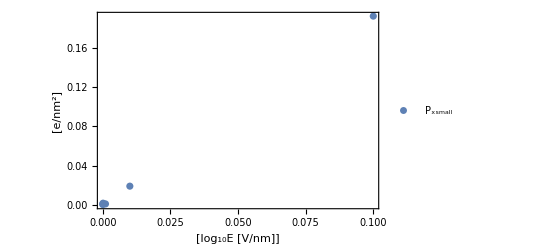

```mathematica
ListPlot[Abs[plotxsmall],PlotRange->All,Frame->True,PlotLegends->{"P_xsmall"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

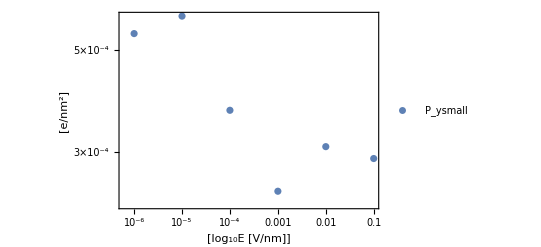

```mathematica
ListLogLogPlot[Abs[plotysmall],PlotRange->All,Frame->True,PlotLegends->{"P_ysmall"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

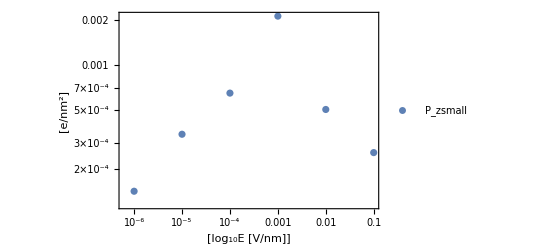

```mathematica
ListLogLogPlot[Abs[plotzsmall],PlotRange->All,Frame->True,PlotLegends->{"P_zsmall"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

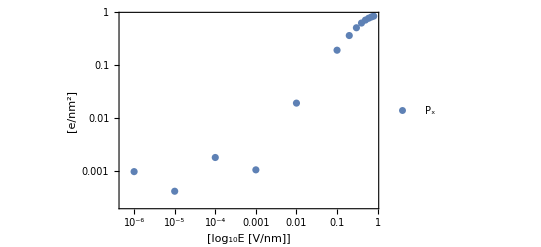

```mathematica
ListLogLogPlot[Abs[plotx],PlotRange->All,Frame->True,PlotLegends->{"P_x"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

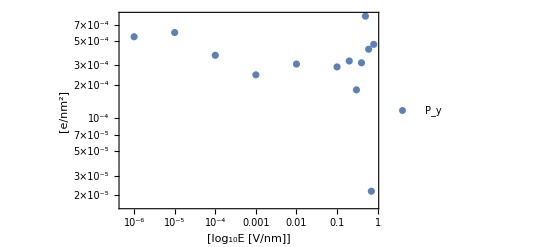

```mathematica
ListLogLogPlot[Abs[ploty],PlotRange->All,Frame->True,PlotLegends->{"P_y"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

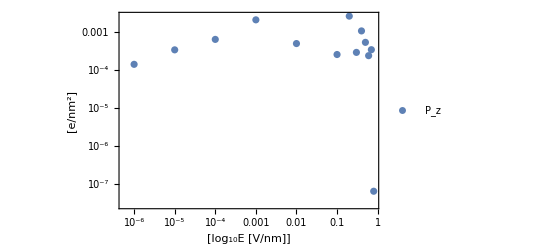

```mathematica
ListLogLogPlot[Abs[plotz],PlotRange->All,Frame->True,PlotLegends->{"P_z"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

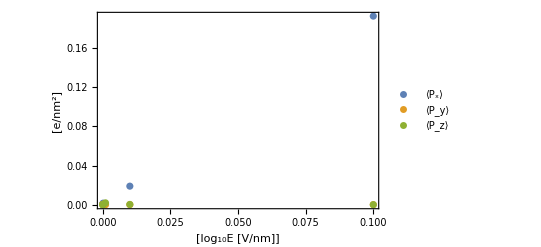

```mathematica
ListPlot[{Abs[plotx],Abs[ploty],Abs[plotz]},PlotRange->All,Frame->True,PlotLegends->{"⟨P_x⟩","⟨P_y⟩","⟨P_z⟩"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

```mathematica
plotx
```

{{1/1000000,-0.000963352},{1/100000,0.000409487},{1/10000,0.00178355},{1/1000,0.00104076},{1/100,0.0191158},{1/10,0.192186},{0.2,0.364338},{0.3,0.511393},{0.4,0.628329},{0.5,0.714956},{0.6,0.774973},{0.7,0.81804},{0.8,0.849479}}

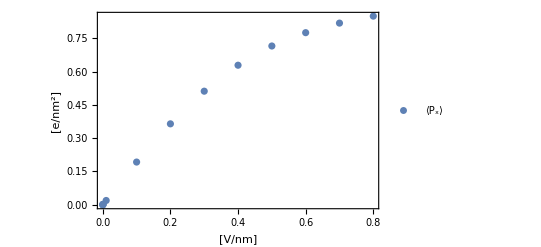

```mathematica
ListPlot[plotx,PlotRange->All,Frame->True,PlotLegends->{"⟨P_x⟩"},FrameLabel->{"[V/nm]","[e/nm^2]"},Filling->{Top,Bottom,0.2}]
```

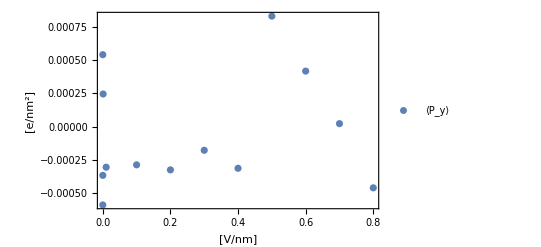

```mathematica
ListPlot[ploty,PlotRange->All,Frame->True,PlotLegends->{"⟨P_y⟩"},FrameLabel->{"[V/nm]","[e/nm^2]"},Filling->{Top,Bottom,0.2}]
```

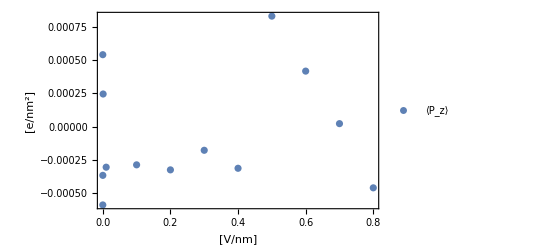

```mathematica
ListPlot[ploty,PlotRange->All,Frame->True,PlotLegends->{"⟨P_z⟩"},FrameLabel->{"[V/nm]","[e/nm^2]"},Filling->{Top,Bottom,0.2}]
```

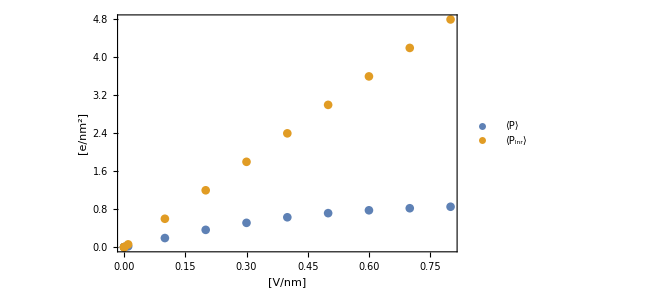

```mathematica
ListPlot[{plotx,plotpubl},PlotRange->All,Frame->True,PlotLegends->{"⟨P⟩","⟨P_lnr⟩"},FrameLabel->{"[V/nm]","[e/nm^2]"},Filling->{Top,Bottom,0.2}]
```

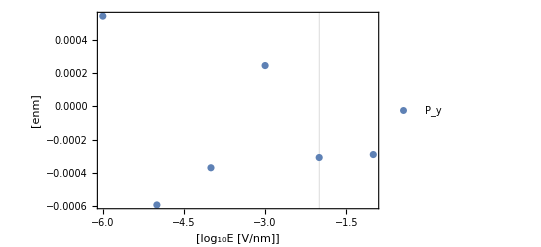

```mathematica
ListPlot[plotlogy,PlotRange->All,Frame->True,PlotLegends->{"P_y"},FrameLabel->{"[log_10E [V/nm]]","[enm]"},GridLines->{{-2},None}]
```

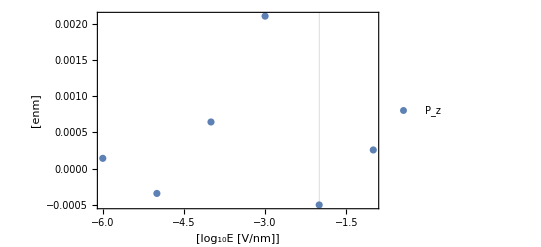

```mathematica
ListPlot[plotlogz,PlotRange->All,Frame->True,PlotLegends->{"P_z"},FrameLabel->{"[log_10E [V/nm]]","[enm]"},GridLines->{{-2},None}]
```

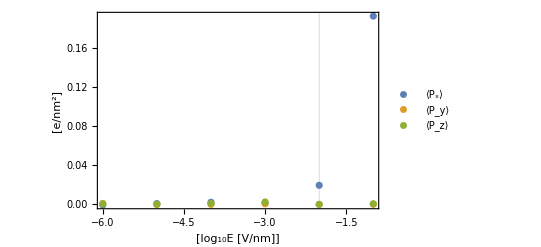

```mathematica
ListPlot[{plotlogx,plotlogy,plotlogz},PlotRange->All,Frame->True,PlotLegends->{"⟨P_x⟩","⟨P_y⟩","⟨P_z⟩"},FrameLabel->{"[log_10E [V/nm]]","[e/nm^2]"},GridLines->{{-2},None}]
```

```mathematica
datasol75=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/0.0-V_nm/dipoles/Mtot_h2o.xvg","Table"]//Drop[#,27]&
```

{{20000,-22.8638,10.557,14.6582,29.1387},{20000.5,16.9756,29.9125,28.2643,44.5174},{20001,4.3899,13.4702,34.3283,37.1369},9995,{24999,-35.1507,-10.8266,29.6348,47.2335},{24999.5,-26.4305,15.0818,22.1185,37.6199},{25000,-34.1234,-8.3318,34.425,49.1824}}
 |  |  |  |

```mathematica
Mean[datasol75[[All,2]]]
Mean[datasol75[[All,3]]]
Mean[datasol75[[All,4]]]
```

-1.1206

-2.11583

1.24259

```mathematica
Mean[data[[All,2]]]
Mean[data[[All,3]]]
Mean[data[[All,4]]]
```

-2.72113

-1.61688

-0.601934

```mathematica
datapureccn=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/25/nvt_pro_run/0.0-V_nm/Mtot.xvg","Table"]//Drop[#,27]&
```

{{20000,-5.24768,-147.448,153.44,212.867},{20000.5,23.8556,7.20931,157.359,159.32},{20001,-22.8474,104.661,-37.2344,113.412},9995,{24999,194.946,34.479,11.3063,198.294},{24999.5,186.797,23.6827,-65.3621,199.314},{25000,203.538,98.5694,-197.374,300.167}}
 |  |  |  |

```mathematica
Mean[datapureccn[[All,2]]]
Mean[datapureccn[[All,3]]]
Mean[datapureccn[[All,4]]]
```

-1.63841

-4.11092

2.13207

```mathematica
eps1=(Mean[(data[[All,5]])^2]-((Mean[data[[All,2]]])^2+(Mean[data[[All,3]]])^2+(Mean[data[[All,4]]])^2))*0.000862793851593755`+1
```

34.3778

```mathematica
eps2=(Mean[(data[[All,5]])^2])*0.000862793851593755`+1
```

34.3868

```mathematica
eps1-eps2
```

-0.0089568

```mathematica
Mean[data[[All,5]]]^2
```

33712.2

```mathematica
Mean[(data[[All,5]])^2]
```

39855.2

```mathematica
eps=(Mean[(data[[All,5]])^2])*0.000862793851593755`+1
```

34.3868

```mathematica
Mean[data[[All,5]]]
```

183.609

```mathematica
dataef=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-6-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
```

```mathematica
eps1=(Mean[(dataef[[All,5]])^2]-((Mean[dataef[[All,2]]])^2+(Mean[dataef[[All,3]]])^2+(Mean[dataef[[All,4]]])^2))*0.000862793851593755`+1
```

33.2256

```mathematica
eps2=(Mean[(dataef[[All,5]])^2])*0.000862793851593755`+1
```

33.2588

```mathematica
eps1-eps2
```

-0.0331313

```mathematica
dataef5=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-5-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
```

```mathematica
eps1ef5=(Mean[(dataef5[[All,5]])^2]-((Mean[dataef5[[All,2]]])^2+(Mean[dataef5[[All,3]]])^2+(Mean[dataef5[[All,4]]])^2))*0.000862793851593755`+1
```

32.477

```mathematica
eps2ef5=(Mean[(dataef5[[All,5]])^2])*0.000862793851593755`+1
```

32.494

```mathematica
eps1ef5-eps2ef5
```

-0.016981

```mathematica
dataef4=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-4-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
```

```mathematica
eps1ef4=(Mean[(dataef4[[All,5]])^2]-((Mean[dataef4[[All,2]]])^2+(Mean[dataef4[[All,3]]])^2+(Mean[dataef4[[All,4]]])^2))*0.000862793851593755`+1
```

33.7705

```mathematica
eps2ef4=(Mean[(dataef4[[All,5]])^2])*0.000862793851593755`+1
```

33.8699

```mathematica
eps1ef4-eps2ef4
```

-0.0994438

```mathematica
dataef3=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-3-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
```

```mathematica
eps1ef3=(Mean[(dataef3[[All,5]])^2]-((Mean[dataef3[[All,2]]])^2+(Mean[dataef3[[All,3]]])^2+(Mean[dataef3[[All,4]]])^2))*0.000862793851593755`+1
```

34.6699

```mathematica
eps2ef3=(Mean[(dataef3[[All,5]])^2])*0.000862793851593755`+1
```

34.8188

```mathematica
eps1ef3-eps2ef3
```

-0.148902

```mathematica
dataef2=Import["/home/tasos/localscratch/asourpis/metadata_MOGON/ccn_h2o_0.25_0.75/75/nvt_pro_run/1e-2-V_nm/dipoles/Mtot.xvg","Table"]//Drop[#,27]&;
```

```mathematica
eps1ef2=(Mean[(dataef2[[All,5]])^2]-((Mean[dataef2[[All,2]]])^2+(Mean[dataef2[[All,3]]])^2+(Mean[dataef2[[All,4]]])^2))*0.000862793851593755`+1
```

32.9639

```mathematica
eps2ef2=(Mean[(dataef2[[All,5]])^2])*0.000862793851593755`+1
```

42.7039

```mathematica
eps1ef2-eps2ef2
```

-9.74

```mathematica
NumberForm[eps,16]
```

1.00000000001077

```mathematica
Mean[dataef[[All,5]]]
```

```mathematica
1.112650021*10^-59/(3*8.854187817*10^-12*118*(10^-9)^3*1.380649*10^-23*298)
```

0.000862794

```mathematica
Simplify[1.112650021 e-59/(-6854+26.562563451 e-1954.998984 (-9+e)^3 e)]
```

1.11265 e-59/(-6854+26.5626 e-1955. (-9.+e)^3 e)

Bulk wate

```mathematica
dataepssurf1=Import["/home/tasos/localscratch/asourpis/gitlab/bulk_water/Mtot_eps_surf_1.xvg","Table"]//Drop[#,27]&
dataepssurfinf=Import["/home/tasos/localscratch/asourpis/gitlab/bulk_water/#Mtot_eps_surf_inf.xvg.1#","Table"]//Drop[#,27]&
```

{{1,-2.72456,0.623275,-7.32852,7.84339},{1.2,9.77762,12.0102,7.37569,17.1537},{1.4,-4.85863,-7.18243,-1.85837,8.86832},49990,{9999.6,2.1015,-2.06383,9.43473,9.88382},{9999.8,-0.505365,-6.83051,19.3729,20.548},{10000,1.27191,1.5149,6.87112,7.15017}}
 |  |  |  |

{{1,-23.4625,-125.606,-4.90113,127.873},{1.2,-9.12676,-98.3639,0.926093,98.7907},{1.4,16.1708,-116.442,6.27729,117.727},49990,{9999.6,-47.3783,46.5138,61.711,90.6448},{9999.8,-37.5531,31.6194,80.6833,94.4448},{10000,-34.1591,12.2066,39.3739,53.5365}}
 |  |  |  |

```mathematica
Mean[dataepssurf1[[All,2]]]
Mean[dataepssurf1[[All,3]]]
Mean[dataepssurf1[[All,4]]]
```

0.00394185

-0.0654892

-0.00687636

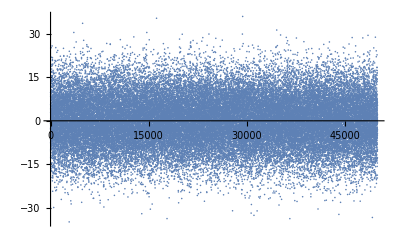

```mathematica
ListPlot[dataepssurf1[[All,2]]]
```

```mathematica
Mean[dataepssurfinf[[All,2]]]
Mean[dataepssurfinf[[All,3]]]
Mean[dataepssurfinf[[All,4]]]
```

1.19927

-0.6072

-2.15007

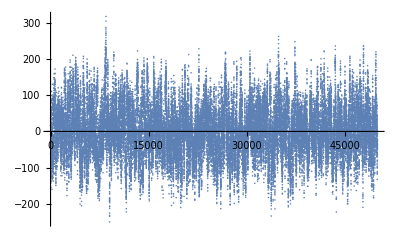

```mathematica
ListPlot[dataepssurfinf[[All,2]]]
```

```mathematica
c=(0.021)^2/((1.38*298/1.602)*10^4)
```

1.71793×10^-10

```mathematica
0.021/1622
```

0.000012947

39855.2

{-2.72113,-1.61688,-0.601934}

{-0.0000352304,-0.0000209338,-7.79324×10^-6}

{{20000,-16.7574,110.272,156.329,192.04},{20000.5,29.7214,118.421,95.9253,155.27},{20001,66.2534,81.8138,35.9748,111.253},9995,{24999,71.5018,-113.741,-62.6312,148.23},{24999.5,55.6013,-27.9047,-149.527,161.952},{25000,29.0733,-77.8374,-157.245,177.848}}
 |  |  |  |

38547.8

{-5.35196,3.02132,0.792565}

{0.0000897519,0.000198161,0.000169305}

{{20000,-50.9915,44.5878,-121.601,139.194},{20000.5,-89.4059,66.2304,-10.9869,111.806},{20001,-233.244,8.30551,57.6328,240.403},9995,{24999,80.5671,-101.035,51.8244,139.23},{24999.5,106.062,-84.6546,143.257,197.327},{25000,161.913,-108.584,112.723,225.195}}
 |  |  |  |

37661.3

{2.27493,-3.29847,-1.90425}

{0.000184913,0.000112755,0.000130806}

{{20000,48.8023,257.799,-59.0186,268.933},{20000.5,187.691,241.863,-85.8221,317.948},{20001,120.393,166.901,-113.021,234.785},9995,{24999,134.549,28.6769,109.141,175.607},{24999.5,79.0494,3.02804,107.443,133.424},{25000,119.08,-69.2716,109.877,176.214}}
 |  |  |  |

39256.1

{9.90861,-2.05431,3.5857}

{0.000289938,0.000135055,0.000208076}

{{20000,52.8362,110.568,63.0231,137.8},{20000.5,-21.1041,118.586,15.5057,121.443},{20001,-79.6284,171.694,-13.4098,189.735},9995,{24999,123.228,99.9205,-64.7972,171.371},{24999.5,141.627,86.3441,18.6039,166.912},{25000,113.712,109.869,63.2227,170.29}}
 |  |  |  |

40355.9

{5.782,1.36733,11.7166}

{0.000240817,0.00018366,0.000317653}

{{20000,43.0172,-92.0909,181.658,208.161},{20000.5,13.2257,-102.661,212.814,236.652},{20001,-28.6612,-139.705,231.534,271.932},9995,{24999,126.576,-80.0856,-55.2471,159.648},{24999.5,113.193,-103.816,28.9362,156.294},{25000,63.2828,4.71778,105.548,123.156}}
 |  |  |  |

49494.9

{106.199,-1.71106,-2.7875}

{0.00153275,0.000135638,0.000121701}

```mathematica
polx={polef6[[1]],polef5[[1]],polef4[[1]],polef3[[1]],polef2[[1]],polef1[[1]]}
poly={polef6[[2]],polef5[[2]],polef4[[2]],polef3[[2]],polef2[[2]],polef1[[2]]}
polz={polef6[[3]],polef5[[3]],polef4[[3]],polef3[[3]],polef2[[3]],polef1[[3]]}
ef={10^-6,10^-5,10^-4,10^-3,10^-2,10^-1};
```

{0.0000897519,0.00158405,0.0162935,0.166032,1.57928,15.9391}

{0.000198161,0.00151189,0.0161386,0.165975,1.57788,15.9252}

{0.000169305,0.00152995,0.0162116,0.166109,1.57787,15.9253}

```mathematica
polx
```

{0.0000897519,0.00158405,0.0162935,0.166032,1.57928,15.9391}

```mathematica
data={polef6[[1]],polef5[[1]],polef4[[1]],polef3[[1]],polef2[[1]],polef1[[1]]}
```

{0.0000897519,0.00158405,0.0162935,0.166032,1.57928,15.9391}

```mathematica
errors={0.434*polerroref6[[1]]/polx[[1]],0.434*polerroref5[[1]]/polx[[2]],0.434*polerroref4[[1]]/polx[[3]],0.434*polerroref3[[1]]/polx[[4]],0.434*polerroref2[[1]]/polx[[5]],0.434*polerroref1[[1]]/polx[[6]]}
```

{0.832337,-0.0139633,-0.00744822,-0.000418507,-0.000829961,-0.000824557}

```mathematica
logx={Log10[ef],Log10[Abs[polx]]}//Transpose
logy={Log10[ef],Log10[Abs[poly]]}//Transpose
logz={Log10[ef],Log10[Abs[polz]]}//Transpose
```

{{-6,-4.04696},{-5,-2.80023},{-4,-1.78799},{-3,-0.779808},{-2,0.198459},{-1,1.20246}}

{{-6,-3.70298},{-5,-2.82048},{-4,-1.79213},{-3,-0.779958},{-2,0.198075},{-1,1.20209}}

{{-6,-3.77133},{-5,-2.81532},{-4,-1.79017},{-3,-0.779607},{-2,0.198071},{-1,1.20209}}

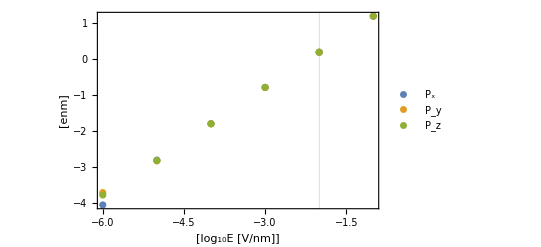

```mathematica
ListPlot[{logx,logy,logz},PlotRange->All,Frame->True,PlotLegends->{"P_x","P_y","P_z"},FrameLabel->{"[log_10E [V/nm]]","[enm]"},GridLines->{{-2},None}]
```

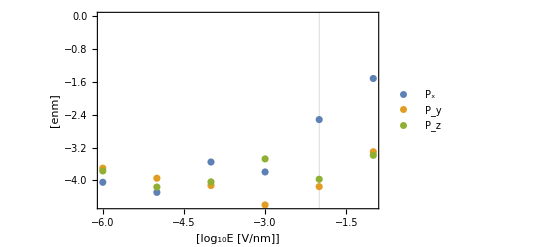

```mathematica
ListPlot[{logx,logy,logz},PlotRange->All,Frame->True,PlotLegends->{"P_x","P_y","P_z"},FrameLabel->{"[log_10E [V/nm]]","[enm]"},GridLines->{{-2},None}]
```

Part::partd: Part specification {0.0000897519,0.00158405,0.0162935,0.166032,1.57928,15.9391}⟦All,2⟧ is longer than depth of object.

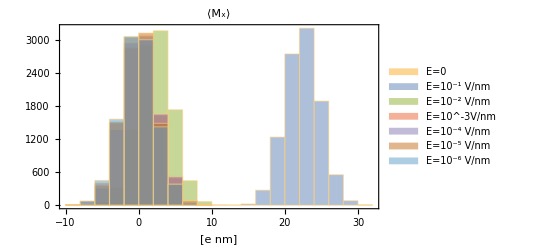

```mathematica
Histogram[{0.021*data[[All,2]],0.021*data1ef1[[All,2]],0.021*data1ef2[[All,2]],0.021*data1ef3[[All,2]],0.021*data1e4[[All,2]],0.021*data1e5[[All,2]],0.021*data1e6[[All,2]]},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

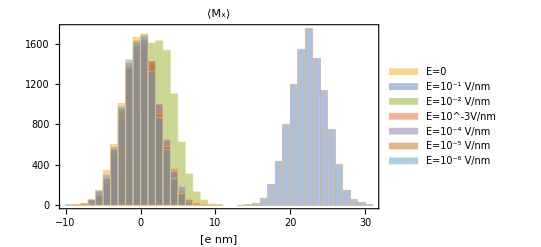

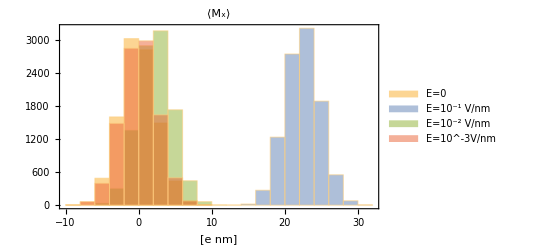

```mathematica
Histogram[{0.021*data[[All,2]],0.021*data1ef1[[All,2]],0.021*data1ef2[[All,2]],0.021*data1ef3[[All,2]]},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

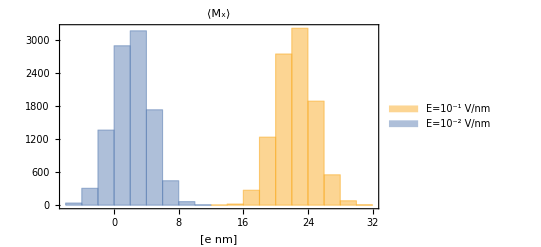

```mathematica
Histogram[{0.021*data1ef1[[All,2]],0.021*data1ef2[[All,2]]},PlotRange->All,Frame->True,ChartLegends->{"E=10^-1 V/nm","E=10^-2 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_x⟩"]
```

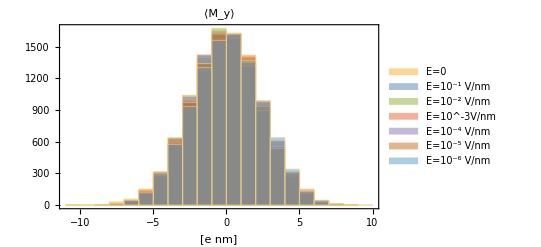

```mathematica
Histogram[{0.021*data[[All,3]],0.021*data1ef1[[All,3]],0.021*data1ef2[[All,3]],0.021*data1ef3[[All,3]],0.021*data1e4[[All,3]],0.021*data1e5[[All,3]],0.021*data1e6[[All,3]]},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_y⟩"]
```

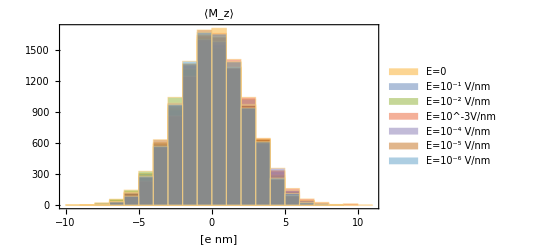

```mathematica
Histogram[{0.021*data[[All,4]],0.021*data1ef1[[All,4]],0.021*data1ef2[[All,4]],0.021*data1ef3[[All,4]],0.021*data1e4[[All,4]],0.021*data1e5[[All,4]],0.021*data1e6[[All,4]]},PlotRange->All,Frame->True,ChartLegends->{"E=0","E=10^-1 V/nm","E=10^-2 V/nm","E=10^-3V/nm","E=10^-4 V/nm","E=10^-5 V/nm","E=10^-6 V/nm"},FrameLabel->{"[e nm]"},PlotLabel->"⟨M_z⟩"]
```